# Set Up Plot Generation for Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/*.dat

## Directory Structures

Current Directory :

```mathematica
workdir="Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/"
```

Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/

```mathematica
workdir
```

Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/

## Data Files

Store all the data file names contained in  workdir:

```mathematica
Files=FileNames["*.dat",workdir]
```

{Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90.dat,Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90-old.dat}

Number of data files in workdir :

```mathematica
Files[[2]]
```

Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90-old.dat

```mathematica
Length[Files]
```

2

Import all data files in workdir :

```mathematica
Data=Import[#,"Table"] &/@Files;
```

```mathematica
Data[[1]]
```

{{3.26231,0.0173074},{2.12702,0.00316669},{4.55364,0.0391062},{1.33676,0.00346643},{1.00218,0.061479},{3.82079,0.00816209},{2.47174,0.0294055},{1.2909,0.0153247},{4.60877,0.0142159},{1.18989,0.330478},{3.51886,0.0191833},{2.69459,0.0162541},{7.09274,0.0239417},{1.04776,0.028929},{3.13311,0.00246708},{2.4806,0.04181},{4.23222,0.0806556},{1.1197,0.0235813},{2.43217,0.0112565},{1.83028,0.118385},{1.61083,0.0726157},{1.57348,0.0485325},{1.35156,0.358313},{1.39272,0.0370902},{2.65555,0.255125},{4.1131,0.086017},{5.57324,0.129914},{1.05974,0.118776},{3.05346,0.00242554},{1.19068,0.0627577},{1.22134,0.044048},{4.26665,0.0100474},{1.26736,0.00015648},{1.10125,0.00219889},{1.49312,0.129945},64277,{1.21008,0.00824624},{4.68328,0.0287137},{1.55929,0.262905},{1.99528,0.0161265},{2.82697,0.0390693},{5.60763,0.00204213},{3.66306,0.289813},{5.58704,0.104064},{1.06673,0.0034893},{6.64659,0.0487317},{2.01363,0.0778806},{1.97925,0.00353768},{3.67428,0.0957461},{3.48232,0.00355342},{2.30281,0.0329462},{4.86666,0.0155157},{3.92571,0.0108333},{1.05024,0.0218161},{1.87803,0.397838},{1.21156,0.590877},{1.34602,0.00342606},{1.12781,0.167784},{2.21704,0.328448},{2.95962,0.00200948},{1.10044,0.0056575},{1.56483,0.113805},{1.69254,0.0103018},{2.74593,0.00732494},{1.61664,0.53518},{2.27768,0.151778},{1.00465,0.246935},{4.40367,0.0196326},{4.66625,0.0444796},{3.54969,0.226643},{2.44175,0.0686463}}
 |  |  |  |

```mathematica
Data[[1,All,1]];
```

## Plots

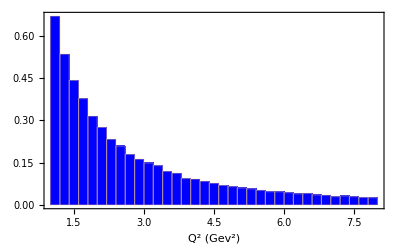

```mathematica
Histogram[Data[[1,All,1]],40,PDF,Frame-> True, FrameLabel->{"Q^2 (Gev^2)"},ChartStyle-> {Blue}]
```

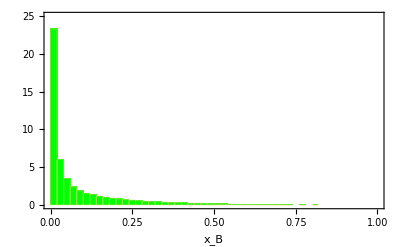

```mathematica
Histogram[Data[[1,All,2]],40,PDF,Frame-> True, FrameLabel->{"x_B"},ChartStyle-> {Green},PlotRange-> {{0,1},{0,25}}]
```